```mathematica
p=(2 σ^2)^(-N/2)2/Gamma[N/2] r^(N-1)Exp[-r^2/(2 σ^2)];
```

```mathematica
Integrate[p,{r,0,∞},Assumptions->{σ ∈ Reals, σ>0,N>0}]
Integrate[r p,{r,0,∞},Assumptions->{σ ∈ Reals, σ>0,N>0}]
Integrate[r^2 p,{r,0,∞},Assumptions->{σ ∈ Reals, σ>0,N>0}]
```

1

(√2 σ Gamma[(1+N)/2])/Gamma[N/2]

N σ^2

```mathematica
FullSimplify[D[p,r]]
```

(2^(1-N/2) ⅇ^(-r^2/(2 σ^2)) r^(-2+N) (σ^2)^(-1-N/2) (-r^2+(-1+N) σ^2))/Gamma[N/2]

```mathematica
Solve[-r^2+(-1+N) σ^2==0,r]
```

{{r→-√(-1+N) σ},{r→√(-1+N) σ}}

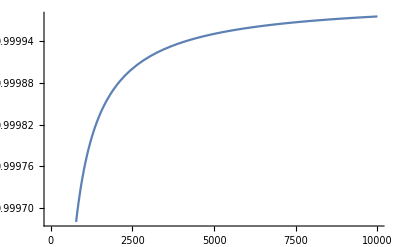

```mathematica
Plot[{√2 Gamma[(1+x)/2]/Gamma[x/2] 1/(√x)},{x,0,10000}]
```

```mathematica
FullSimplify[N σ^2-((√2 σ Gamma[(1+N)/2])/Gamma[N/2])^2]
```

σ^2 (N-(2 Gamma[(1+N)/2]^2)/Gamma[N/2]^2)

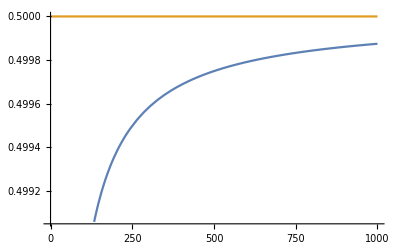

```mathematica
Plot[{x-(2 Gamma[(1+x)/2]^2)/Gamma[x/2]^2,1/2},{x,0,1000}]
```